```mathematica
Clear[pts1, pts2, data1, data2, m]
Λ=0.15; μ=0.5; c=1;d=3;
min = 0.8; max = 1.4; dM2=0.05;W2=2.1;
a[M2_, 1]:=(4π)/9 1/Log[M2/Λ^2]
a[M2_,2]:=0.35;
L[M2_, 1]:=((M2/Λ^2)/Log[μ^2/Λ^2])^(4/9)
L[M2_, 2]:=(Log[M2/Λ]/Log[μ/Λ])^(4/9)
L[M2_, 3]:=(a[μ^2, c]/a[M2, c])^(4/9)
f1[M2_, W2_]:=M2^3/L[M2, d](1-E^(-W2/M2)(1+W2/M2+W2^2/(2 M2^2)))+0.5 M2/(4 L[M2, d])(1-E^(-W2/M2))+
	4/3 0.55^2 L[M2, d]+-1/3 0.8 0.55^2 1/M2
f2[M2_, W2_]:=1.1 M2^2(1-E^(-W2/M2)(1+W2/M2))+
-0.55 0.5/12+ 272/81 a[M2, c]/π 0.55^3/M2 
Timing[
pts1 = Table[f1[M2, 2.5],{M2,min,max, dM2}] ;
]
data1 = Transpose[Join[{Range[min, max, dM2]}, {pts1}]];
FindFit[data1,λ2 E^(-m1^2/M2), {λ2,m1}, M2]
Timing[
pts2 = Table[f2[M2, W2],{M2,min,max, dM2}] ;
]
data2 = Transpose[Join[{Range[min, max, dM2]}, {pts2}]];
FindFit[data2,m2 λ22 E^(-m2^2/M2), {λ22,m2}, M2]
m[M2_,W2_]:= f2[M2, W2]/f1[M2, W2]
```

{0.015,Null}

{λ2→2.12331,m1→0.936077}

{8.94467×10^-19,Null}

{λ22→1.9624,m2→0.988434}

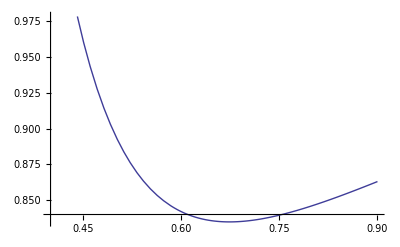
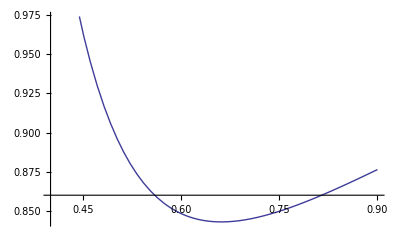
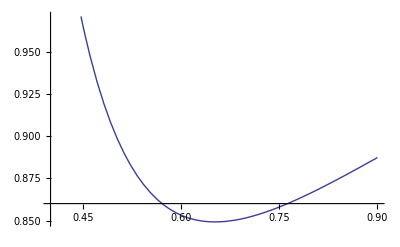
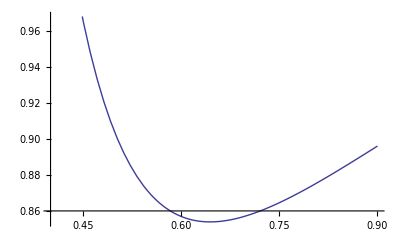
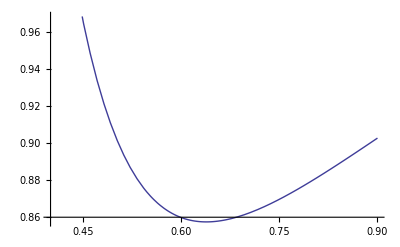
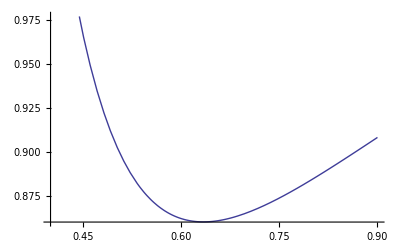
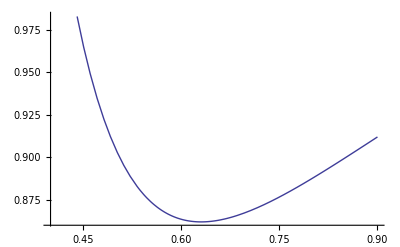
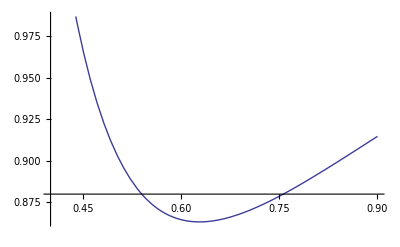

```mathematica
Table[Plot[m[M2, W2], {M2, 0.4, 0.9}], {W2,1.8,2.7,0.1}]
```

```mathematica
Clear[a, m, g1, g2, pts3, pts4]
a=0.546; m02=0.5;
g1[M2_]:=M2^3+4/3 a^2
g2[M2_]:=2 a M2^2(1+1/2 m02/M2)
mnucl[M2_]:=g2[M2]/g1[M2]
Timing[
pts3 = Table[g1[M2]+g2[M2],{M2,min,max, 0.1}] ;
]
data3 = Transpose[Join[{Range[min, max, 0.1]}, {pts3}]];
FindFit[data3,(m+1)λ2 E^(-m^2/M2), {λ2,m}, M2]
```

{0.,Null}

{λ2→11.254,m→1.51646}

```mathematica
Clear[a, m, g1, g2, pts3, pts, data]
a=0.546; m02=0.5;min = 0.8; max = 1.4; dM2=0.05
g1[M2_]:=Log[M2^3+4/3 a^2]M2
g2[M2_]:=Log[2 a M2^2(1+1/2 m02/M2)]M2
Timing[
pts = Table[g2[M2],{M2,min,max, dM2}] ;
]
data = Transpose[Join[{Range[min, max, dM2]}, {pts}]];
FindFit[data,a1+b M2, {a1,b}, M2]
```

0.05

{0.,Null}

{a1→-1.94636,b→2.28151}